```mathematica
Clear["Global`*"]
```

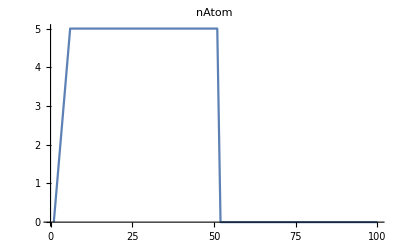

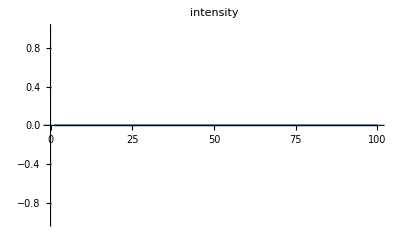

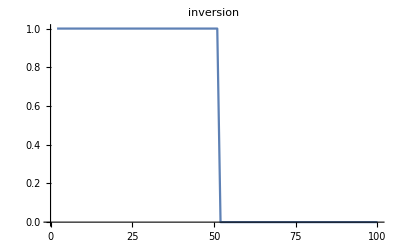

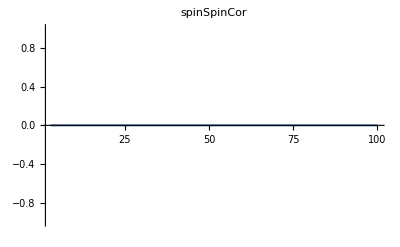

```mathematica
(*When doing one run*)
name ="oneRun_N050_meanGen1_tau1_Traj1";
intensityy=Flatten[Import[NotebookDirectory[]<>name<>"/intensity.dat"]];
nAtomm=Flatten[Import[NotebookDirectory[]<>name<>"/nAtom.dat"]];
inversionn=Flatten[Import[NotebookDirectory[]<>name<>"/inversion.dat"]];
spinSpinCorr=Flatten[Import[NotebookDirectory[]<>name<>"/spinSpinCor.dat"]];
ListLinePlot[nAtomm,PlotRange->All,PlotLabel->nAtom]
ListLinePlot[intensityy,PlotRange->All,PlotLabel->intensity]
ListLinePlot[inversionn,PlotRange->All,PlotLabel->inversion]
ListLinePlot[spinSpinCorr,PlotRange->All,PlotLabel->spinSpinCor]
```

```mathematica
inversionn
```

{nan,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
L=Table[0,{i,20}];
```

```mathematica
For[i=0,i<20,i++,
x=Flatten[Import[NotebookDirectory[]<>"meanP"<>ToString[i]<>"/nAtom.dat"]];
x=Cases[x,Except[0|0.]];
L[[i+1]]=Last[x];
]
```

Import::nffil: File not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

```mathematica
nAtomSS=Flatten[Import["/Users/westgatesnow/Desktop/Codes/2017/beamLaser/versusTau/nAtomSS.dat"]];
```

Import::nffil: File not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

```mathematica
nAtomSS
```

Flatten[$Failed]

```mathematica
L
```

{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}

```mathematica
ListLinePlot[L]
```

-Graphics-

```mathematica
gc=1
```

1

```mathematica
Clear[gc,a]
```

```mathematica
a={{0,0.5gc,0,0,0.5gc,0},{0.5gc,0,0,0.5gc,0,0},{0,0,4gc,0,0,0},{0,0.5gc,0,0,0.5gc,0},{0.5gc,0,0,0.5gc,0,0},{0,0,0,0,0,4gc}}//MatrixForm
Eigenvalues[%]
```

(0 | 0.5 gc | 0 | 0 | 0.5 gc | 0
0.5 gc | 0 | 0 | 0.5 gc | 0 | 0
0 | 0 | 4 gc | 0 | 0 | 0
0 | 0.5 gc | 0 | 0 | 0.5 gc | 0
0.5 gc | 0 | 0 | 0.5 gc | 0 | 0
0 | 0 | 0 | 0 | 0 | 4 gc)

{4. gc,4. gc,-1. gc,1. gc,-1.67735×10^-17 gc,1.67735×10^-17 gc}